```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection[JDBC["SQLite","/home/daniel/exp/loopspeed/log.db"]]
```

SQLConnection[…]

```mathematica
list=SQLExecute[conn,"SELECT name FROM log GROUP BY name"];
```

```mathematica
data=Table[{i[[1]],SQLExecute[conn,"SELECT size,time FROM log WHERE name='"<>ToString[i[[1]]]<>"'"]},{i,list}];
```

```mathematica
data//Length
```

16

```mathematica
data[[13,1]]
```

inc.r

inc.js

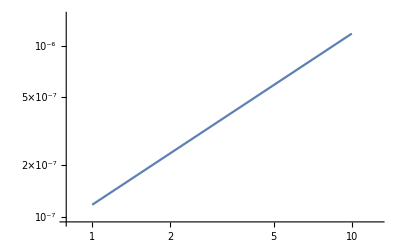

```mathematica
data[[7,1]]
```

```mathematica
Exp[a Log[x] + b]/.eps[[1]]
```

3.58554×10^-6 x^1.0108

```mathematica
Table[Show[{ListLogLogPlot[{data[[i,2]]},PlotRange->Full,PlotLabel->data[[i,1]],BaseStyle->{FontSize->11}],LogLogPlot[Exp[a Log[x] + b]/.eps[[i]],{x,1,10^11}]}],{i,1,16}];
```

```mathematica
lps[[1]]
```

{a→-12.4092,b→-1.97465×10^-9}

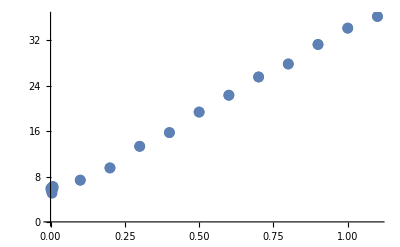

```mathematica
ListPlot[data[[8,2]]]
```

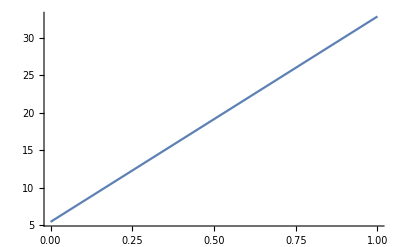

```mathematica
Plot[Exp[a] x+ b^2/.lps[[8]],{x,1,10^10}]
```

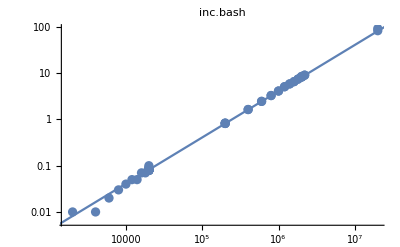
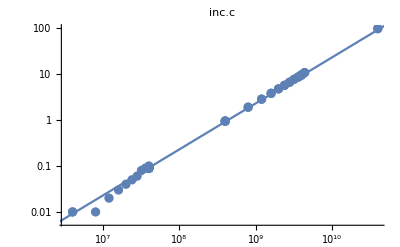
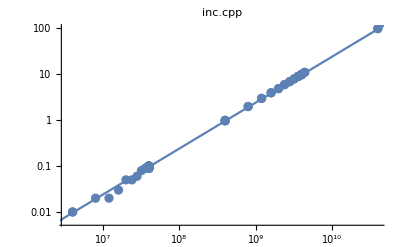
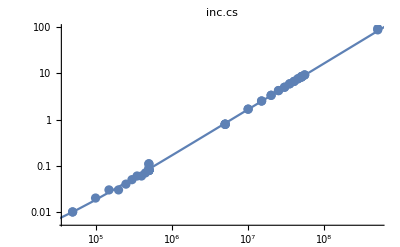
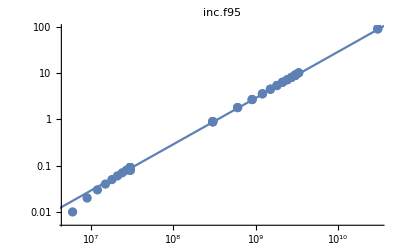
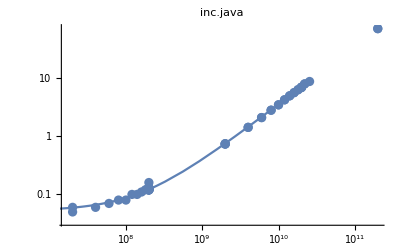
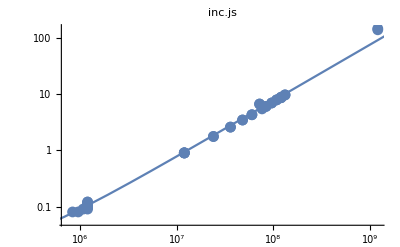
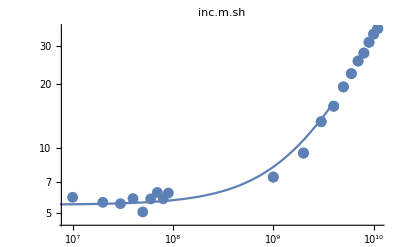

```mathematica
Table[Show[{ListLogLogPlot[{data[[i,2]]},PlotRange->Full,PlotLabel->data[[i,1]],BaseStyle->{FontSize->11}],LogLogPlot[Exp[a]x + b^2/.lps[[i]],{x,1,10^11}]}],{i,1,16}]
```

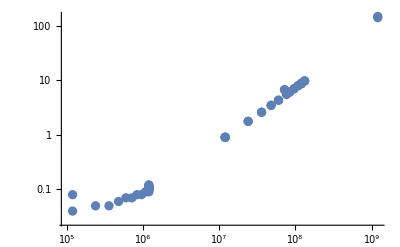

```mathematica
ListLogLogPlot[{data[[7,2]]},PlotRange->All]
```

```mathematica
Drop[data,{8}][[All,1]]
```

{inc.bash,inc.c,inc.cpp,inc.cs,inc.f95,inc.java,inc.js,inc.p,inc.perl,inc.php,inc.python,inc.r,inc.rb,inc.sql.sh,inc.wl}

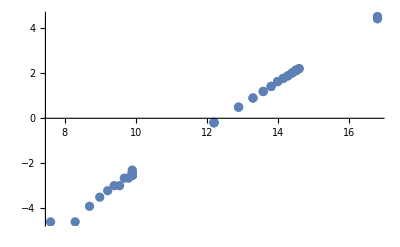

```mathematica
ListPlot[Log[data[[1,2]]]]
```

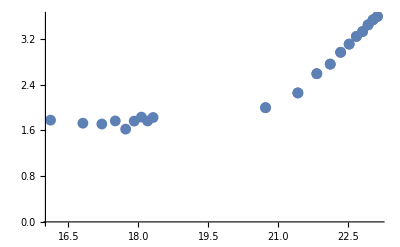

```mathematica
ListPlot[Log[data[[8,2]]]]
```

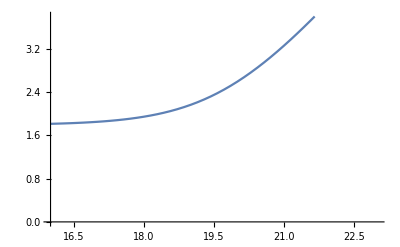

```mathematica
Plot[Log[Exp[a] Exp[x]+b]/.{a->-18,b->6},{x,16,23},PlotRange->{0,3.8}]
```

```mathematica
eps8=FindFit[Log[data[[8,2]]],Log[Exp[a] Exp[x]+b^2],{a,b},x]
```

{a→-19.7161,b→2.33828}

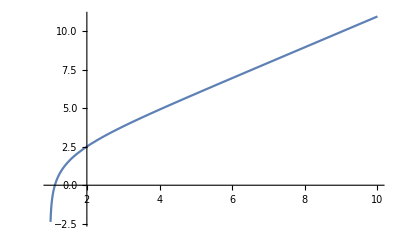

```mathematica
Plot[Log[a Exp[x] + b]/.eps8,{x,1,10}]
```

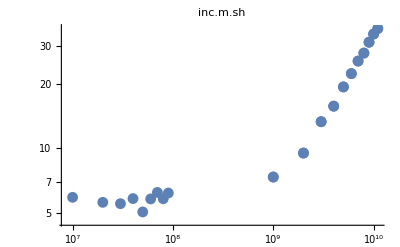

```mathematica
Show[{ListLogLogPlot[{data[[8,2]]},PlotRange->Full,PlotLabel->data[[8,1]],BaseStyle->{FontSize->11}],LogLogPlot[Exp[a Log[x] + b]/.eps8,{x,1,10}]}]
```

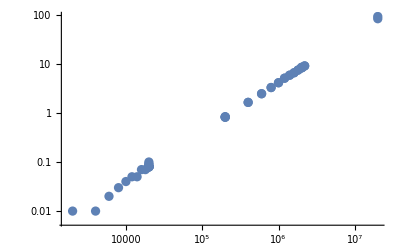

```mathematica
ListLogLogPlot[data[[1,2]]]
```

```mathematica
eps=FindFit[Log[data[[#,2]]],a x+b,{a,b},x]&/@Range[16] (*time per one execution*)
```

{{a→1.0108,b→-12.5386},{a→1.02018,b→-20.2889},{a→1.0124,b→-20.0904},{a→0.996392,b→-15.5385},{a→1.01827,b→-20.015},{a→0.821773,b→-17.6269},{a→0.985028,b→-16.0814},{a→0.282043,b→-3.27765},{a→1.01511,b→-20.3332},{a→1.01003,b→-17.3368},{a→0.937131,b→-17.2933},{a→0.978163,b→-16.2027},{a→0.552607,b→-8.86356},{a→0.883608,b→-14.9442},{a→0.964381,b→-12.5287},{a→0.69641,b→-9.52756}}

```mathematica
lps=FindFit[Log[data[[#,2]]],Log[Exp[a] Exp[x]+b^2],{a,b},x]&/@Range[data//Length]
```

{{a→-12.4092,b→-1.97465×10^-9},{a→-19.8955,b→3.75384×10^-9},{a→-19.8486,b→1.30791×10^-10},{a→-15.6123,b→-0.0407829},{a→-19.661,b→-5.82143×10^-8},{a→-21.7757,b→-0.228557},{a→-16.3811,b→-0.111687},{a→-19.7161,b→2.33828},{a→-20.036,b→2.05876×10^-9},{a→-17.169,b→1.46371×10^-8},{a→-18.5471,b→-0.113533},{a→-16.6034,b→-0.0752874},{a→-17.1484,b→0.395382},{a→-17.1357,b→0.186794},{a→-13.0417,b→0.0803551},{a→-14.5368,b→-0.451926}}

```mathematica
tps=Fit[Drop[data,{8}][[#,2]],{x},x]&/@Range[15]/x (*time per one execution*)
```

{4.3682×10^-6,2.42609×10^-9,2.46948×10^-9,1.79912×10^-7,2.99193×10^-9,3.52285×10^-10,1.17821×10^-7,2.05391×10^-9,3.57987×10^-8,8.58989×10^-9,6.24234×10^-8,9.61642×10^-8,3.62218×10^-8,2.21022×10^-6,5.04557×10^-7}

```mathematica
Transpose[{Drop[data,{8}][[All,1]],Round[4.5/(50tps)]}]//TableForm
```

inc.bash | 20603
inc.c | 37096746
inc.cpp | 36444871
inc.cs | 500246
inc.f95 | 30080875
inc.java | 255474694
inc.js | 763872
inc.p | 43818817
inc.perl | 2514055
inc.php | 10477431
inc.python | 1441766
inc.r | 935899
inc.rb | 2484689
inc.sql.sh | 40720
inc.wl | 178374

```mathematica
opi={20000,40000000,40000000,500000,30000000,200000000,1200000,1200000,1200000,2500000,2500000,10000000,30000000,40000000,200000000};
opi*tps*50
```

{4.36943,4.85263,4.93909,4.49887,4.48811,3.52372,7.0745,0.123243,2.14661,1.07379,7.80455,16.7155,54.3361,4421.17,5045.92}

{0.436943,0.000485263,0.00246955,0.449887,0.00179525,0.00211423,0.70745,0.0256757,0.447211,0.429517,9.36545,6.68618,7.24482,442.117,504.592}

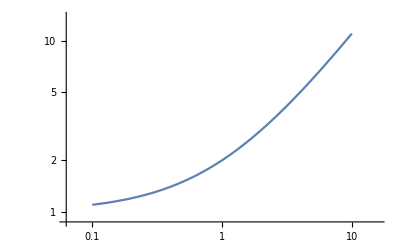

```mathematica
LogLogPlot[1+x,{x,.1,10}]
```

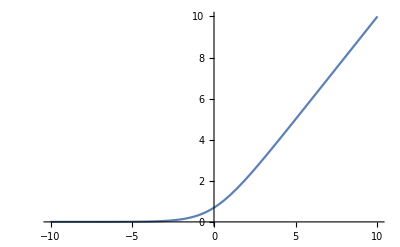

```mathematica
Plot[Log[+1+Exp[x]],{x,-10,10}]
```